# X plane

## Import

### Ground truth

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"UTILITY_readBeamFiles.nb"}]];
fileName= FileNameJoin[{NotebookDirectory[],"2025-03-25_groundTruth.h5"}];
data = readBeamFile[fileName];
```

```mathematica
rawTruth = 10^3{#x,#px/#pz}&/@data;
```

```mathematica
rawTruth =BinCounts[rawTruth,{-0.25,0.25,0.0005},{-0.25,0.25,0.0005}];
```

```mathematica
ArrayPlot[Reverse[Transpose[rawTruth]],ColorFunction->"Rainbow"]
```

-Graphics-

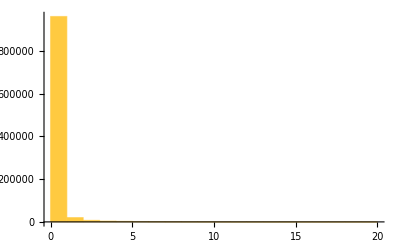

```mathematica
Histogram[Flatten[rawTruth]]
```

### Reconstruction

Edges span -0.25 to 0.25 in steps of 0.0005

```mathematica
rawReconstruction = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/reconstruction_X.csv"];
ArrayPlot[Reverse[Transpose[rawReconstruction]],ColorFunction->"Rainbow"]
```

-Graphics-

## Process

```mathematica
blurRad = 20;
processedTruth = GaussianFilter[rawTruth,5];
processedReconstruction =  GaussianFilter[rawReconstruction,5];

processedTruth = processedTruth / Total[Flatten[processedTruth]];
processedReconstruction = processedReconstruction / Total[Flatten[processedReconstruction]];

scaleFactor = 1*^4;

ArrayPlot[scaleFactor*Reverse[Transpose[processedTruth]],ColorFunction->"Rainbow",ColorFunction->"Rainbow",PlotLegends->Automatic,ColorFunctionScaling->False,ImageSize->600,LabelStyle->20]
ArrayPlot[scaleFactor*Reverse[Transpose[processedReconstruction]],ColorFunction->"Rainbow",ColorFunction->"Rainbow",PlotLegends->Automatic,ColorFunctionScaling->False,ImageSize->600,LabelStyle->20]
```

-Graphics-

-Graphics-

```mathematica
ArrayPlot[scaleFactor*Reverse[Transpose[processedTruth-processedReconstruction]],ColorFunction->"Rainbow",ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->600,LabelStyle->20]
```

-Graphics-

```mathematica
Mean[Flatten[processedTruth]]
```

1.×10^-6

```mathematica
Mean[Flatten[Abs[processedTruth-processedReconstruction]]]
```

4.01179×10^-7

## Reconstruct population

```mathematica
xyReconstruction=Table[
{
-0.25 + xII * 0.0005,
-0.25 + yII * 0.0005,
rawReconstruction[[xII,yII]]
},

{xII, Length[rawReconstruction]},
{yII, Length[rawReconstruction]}
];
xyReconstruction = Flatten[xyReconstruction,1];
Length[xyReconstruction]
```

1000000

```mathematica
maxVal = Max[xyReconstruction[[All,3]]]
xyReconstruction = {#[[1]],#[[2]],#[[3]]/maxVal}&/@xyReconstruction;
```

8029.

```mathematica
ListDensityPlot[RandomSample[xyReconstruction,50000],ColorFunction->"Rainbow",PlotRange->All]
```

-Graphics-

```mathematica
interp=Interpolation[xyReconstruction,InterpolationOrder->0]
```

InterpolatingFunction[{{-0.2495, 0.25}, {-0.2495, 0.25}}, <>]

```mathematica
population={};

While[
Length[population]<100000,
{x,y}=RandomReal[{-0.25,0.25},2];

If[
RandomReal[]<interp[x,y],
AppendTo[population,{x,y}]
]
];
```

InterpolatingFunction::dmval: Input value {0.193879,-0.249926} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.108117,-0.249869} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.155467,-0.24972} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

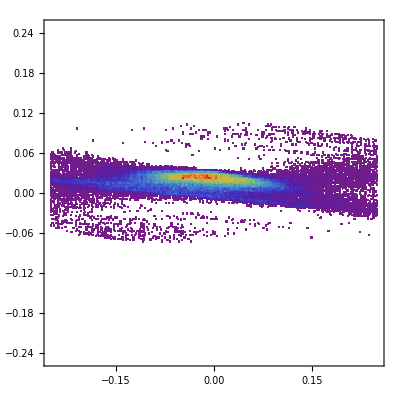

```mathematica
binSize = 0.002;
DensityHistogram[population,{{binSize},{binSize}},ColorFunction->"Rainbow",PlotRange->{{-0.25,0.25},{-0.25,0.25}}]
```

```mathematica
Export["~/reconstruction_X.csv",population]
```

~/reconstruction_X.csv

# Y plane

## Import

### Ground truth

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"UTILITY_readBeamFiles.nb"}]];
fileName= FileNameJoin[{NotebookDirectory[],"2025-03-25_groundTruth.h5"}];
data = readBeamFile[fileName];
```

```mathematica
rawTruth = 10^3{#y,#py/#pz}&/@data;
```

```mathematica
rawTruth =BinCounts[rawTruth,{-0.25,0.25,0.0005},{-0.25,0.25,0.0005}];
```

```mathematica
ArrayPlot[Reverse[Transpose[rawTruth]],ColorFunction->"Rainbow"]
```

-Graphics-

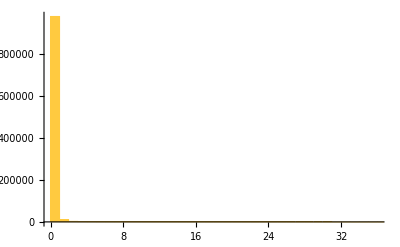

```mathematica
Histogram[Flatten[rawTruth]]
```

### Reconstruction

Edges span -0.25 to 0.25 in steps of 0.0005

```mathematica
rawReconstruction = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/reconstruction_Y.csv"];
ArrayPlot[Reverse[Transpose[rawReconstruction]],ColorFunction->"Rainbow"]
```

-Graphics-

## Process

```mathematica
blurRad = 20;
processedTruth = GaussianFilter[rawTruth,5];
processedReconstruction =  GaussianFilter[rawReconstruction,5];

processedTruth = processedTruth / Total[Flatten[processedTruth]];
processedReconstruction = processedReconstruction / Total[Flatten[processedReconstruction]];

scaleFactor = 0.3*^4;

ArrayPlot[scaleFactor*Reverse[Transpose[processedTruth]],ColorFunction->"Rainbow",ColorFunction->"Rainbow",PlotLegends->Automatic,ColorFunctionScaling->False,ImageSize->600,LabelStyle->20]
ArrayPlot[scaleFactor*Reverse[Transpose[processedReconstruction]],ColorFunction->"Rainbow",ColorFunction->"Rainbow",PlotLegends->Automatic,ColorFunctionScaling->False,ImageSize->600,LabelStyle->20]
```

-Graphics-

-Graphics-

```mathematica
ArrayPlot[scaleFactor*Reverse[Transpose[processedTruth-processedReconstruction]],ColorFunction->"Rainbow",ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->600,LabelStyle->20]
```

-Graphics-

```mathematica
Mean[Flatten[processedTruth]]
```

1.×10^-6

```mathematica
Mean[Flatten[Abs[processedTruth-processedReconstruction]]]
```

5.18501×10^-7

## Reconstruct population

```mathematica
xyReconstruction=Table[
{
-0.25 + xII * 0.0005,
-0.25 + yII * 0.0005,
rawReconstruction[[xII,yII]]
},

{xII, Length[rawReconstruction]},
{yII, Length[rawReconstruction]}
];
xyReconstruction = Flatten[xyReconstruction,1];
Length[xyReconstruction]
```

1000000

```mathematica
maxVal = Max[xyReconstruction[[All,3]]]
xyReconstruction = {#[[1]],#[[2]],#[[3]]/maxVal}&/@xyReconstruction;
```

13711.

```mathematica
ListDensityPlot[RandomSample[xyReconstruction,50000],ColorFunction->"Rainbow",PlotRange->All]
```

-Graphics-

```mathematica
interp=Interpolation[xyReconstruction,InterpolationOrder->0]
```

InterpolatingFunction[{{-0.2495, 0.25}, {-0.2495, 0.25}}, <>]

```mathematica
population={};

While[
Length[population]<100000,
{x,y}=RandomReal[{-0.25,0.25},2];

If[
RandomReal[]<interp[x,y],
AppendTo[population,{x,y}]
]
];
```

InterpolatingFunction::dmval: Input value {-0.173962,-0.249741} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0466526,-0.249983} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0873558,-0.249509} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

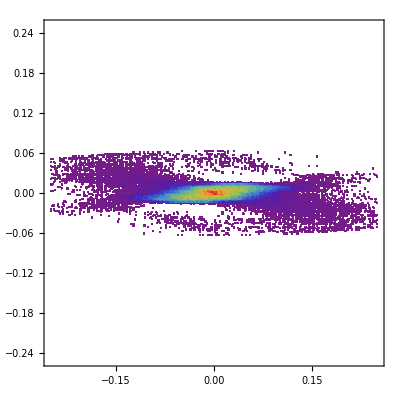

```mathematica
binSize = 0.002;
DensityHistogram[population,{{binSize},{binSize}},ColorFunction->"Rainbow",PlotRange->{{-0.25,0.25},{-0.25,0.25}}]
```

```mathematica
Export["~/reconstruction_Y.csv",population]
```

~/reconstruction_Y.csv